```mathematica
SetDirectory[NotebookDirectory[]];
meta=Uncompress@Get["metadata.dat"];
ids=Drop[Import["genbank_ids_2016June25.csv"],1];
{meta//Dimensions,ids//Dimensions}
```

{{34743,4},{32058,4}}

```mathematica
(*{meta[[1]],ids[[1]]}*)
```

```mathematica
Print[Dynamic[s]];s=0;
allids=ids[[;;,1]];
associds=Association[#[[1]]->#&/@ids];
fullmeta={s+=1;s,
#[[1]],
#[[2]],
#[[3]],
If[KeyExistsQ[associds,#[[2]]],associds[#[[2]]],{}]
}&/@meta;
```

```mathematica
(*{associds["AB055387.1"],fullmeta[[1]]}*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
ptsUnscaled=Uncompress@Get["mds5-manhat.dat"];
pts=Transpose[Rescale[#,{Min[#],Max[#]},{-1,1}]&/@Transpose[ptsUnscaled]];
(*ListPointPlot3D[RandomChoice[pts,Length@pts][[;;,{1,2,3}]],BoxRatios->{1, 1, 1},PlotRange->All];*)
pts//Dimensions
```

{34743,5}

```mathematica
(*{{"H",7085},{"L",4007},{"M",3029},{"U",2764},{"B",2332},{"D",1673},{"J",1485},{"T",1441},{"K",1435},{"C",1047},{"A",942},{"R",737},{"F",604},{"N",559},{"I",487},{"V",471},{"W",379},{"X",335},{"E",262},{"G",254},{"Q",164},{"Z",141},{"Y",123},{"P",86},{"S",14},{"O",4}}*)haplo={"B","X","H","S","M","G","L","C","A","F","T","J","D","U","P","Q","V","N","W","K","I","R","Z","Y","E","O"};
haplo={"O","S"};
haplo={"H","L","M","U","B","D","J","T","K","C","A","R","F","N","I","V","W","X","E","G","Q","Z","Y"};
```

```mathematica
ls=StringTake[#,{1,Min[2,StringLength[#]]}]&/@haplometa[[;;,5,4]];
ls;
```

```mathematica
Sort[Tally[ls],#1[[2]]>#2[[2]]&];
```

```mathematica
(* Sample Accession NUmbers *)
SeedRandom[12345];
haplometa  = Select[fullmeta,Length@#[[5]]>0&];
haploIndices=Table[
tmp=Select[haplometa,(StringTake[#[[5,3]],{1,Min[StringLength@haplo[[i]],StringLength[#[[5,3]]]]}]==haplo[[i]])&&(#[[4]]>16000)&];
RandomSample[tmp[[;;,1]],(**)100]
,{i,1,Length@haplo}];
allhaploindices=Flatten@haploIndices;
```

```mathematica
newDir="ref_23_100_greater16k";(* NEW DIR *)
SetDirectory[NotebookDirectory[]];
If[!FileExistsQ[newDir],CreateDirectory[newDir]];
SetDirectory[newDir];
```

```mathematica
(* Download files *)
Print[{Dynamic[i],Length@allhaploindices}];
SetDirectory[NotebookDirectory[]];
If[!FileExistsQ[newDir],CreateDirectory[newDir]];SetDirectory[newDir];
If[!FileExistsQ["fasta"],CreateDirectory["fasta"]];SetDirectory["fasta"];
Table[
tmpAcc=fullmeta[[allhaploindices[[i]],3]];
URLSave["http://eutils.ncbi.nlm.nih.gov/entrez/eutils/efetch.fcgi?db=nuccore&rettype=fasta&retmode=text&id="<>tmpAcc,FileNameJoin[{Directory[],tmpAcc<>".fasta"}]];
,{i,1,Length[allhaploindices]}];
```

{,2300}

```mathematica
(* SAVE INFO *)
SetDirectory[NotebookDirectory[]];SetDirectory[newDir];out="";
(out=out<>#[[1]]<>"\n"<>ToString[#[[2]]]<>"\n\n")&/@Transpose[{haplo,haploIndices}];
Export["haploinfo.txt",out];
```

```mathematica
(* CGR READ-BUILD *)
SetDirectory[NotebookDirectory[]];Needs["GenResearch`"];
SetDirectory[newDir];cgrOrder={"A","C","G","T"};k=9;
curFileNamesOrder=fullmeta[[#,3]]<>".fasta"&/@allhaploindices;
Export["cgrFileOrder.txt",curFileNamesOrder];
```

```mathematica
newDir
```

ref_23_100_greater16k

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],newDir,"fasta"}]];
Print[AbsoluteTiming[Monitor[allCGRs = {}; flnames =curFileNamesOrder;
For[i = 1, i ≤ Length[flnames], i++, 
	
	nextNewCGR = linearCGRgrayscale[Import[flnames[[i]]][[1]], cgrOrder, k];

	(*nextNewCGR = sparseFCGR[Import[flnames[[i]]][[1]], cgrOrder, k][[2]];
	newCGRList=Table[nextNewCGR[[i1,1]]->nextNewCGR[[i1,2]],{i1,1,Length@nextNewCGR}];
    nextNewCGR=SparseArray[newCGRList,{2^k,2^k}];*)

	AppendTo[allCGRs, nextNewCGR];
];
,
TableForm[{StringJoin["Reading file: ", ToString[{i,Length[flnames]}], " - ", flnames[[i]]], 
ProgressIndicator[Dynamic[i], {1, Length[flnames]}]}]];
"reading "<>ToString[i-1]<>" files"]];
```

{248.872,reading 2300 files}

```mathematica
SetDirectory[NotebookDirectory[]];SetDirectory[newDir];Put[Compress@allCGRs,"allCGRs.dat"];Dimensions@allCGRs
```

{2300,512,512}

```mathematica
(*SetDirectory[NotebookDirectory[]];SetDirectory[newDir];allCGRs=Uncompress@Get["allCGRs.dat"];Dimensions@allCGRs*)
```

$Aborted

```mathematica
curHaploOrder=associds[[First[StringSplit[#,".fasta"]]]][[3]]&/@curFileNamesOrder;
```

```mathematica
filteredHaplo = Select[haplometa,MemberQ[haplo,StringTake[#[[5,3]],{1,1}]]&];
filteredHaplo//Dimensions
```

{31756,5}

```mathematica
Print[Dynamic[{"C=",totCor,"W=",totWro,"T=",total,"top5=",totTOP5,Length@filteredHaplo,N[100*totCor/total,4],curAcc}]];
totCor=0;totWro=0;total=0;totTOP5=0;
For[haplometaINDEX=1,haplometaINDEX≤Length@filteredHaplo,haplometaINDEX++,
curAcc=filteredHaplo[[haplometaINDEX,3]];
(*Print[curAcc];*)
(*curFilePath=URLSave["http://eutils.ncbi.nlm.nih.gov/entrez/eutils/efetch.fcgi?db=nuccore&rettype=fasta&retmode=text&id="<>curAcc,FileNameJoin[{$TemporaryDirectory,curAcc<>".fasta"}]];*)
curFilePath=FileNameJoin[{NotebookDirectory[],"allfiles",curAcc<>".fasta"}];
(*Print[curFilePath];*)
(*curFileSeq=First@Import[FileNameJoin[{$TemporaryDirectory,curAcc<>".fasta"}]];*)
curFileSeq=First@Import[curFilePath];
(*Print[curFileSeq];*)
curCGR = linearCGRgrayscale[curFileSeq, cgrOrder, k];
(**)
(*Print[{curFilePath,StringLength@curFileSeq,Dimensions@curCGR}];*)
(**)
newDists=Table[
ApproxInfoDist[curCGR,allCGRs[[i]]]
,{i,1,Length@allCGRs}];
tmp=Mean[#]&/@Partition[newDists,100(**)];
pos=Position[tmp,Min[tmp]][[1,1]];
(*Print@Sort[Transpose[{haplo,tmp}],#1[[2]]<#2[[2]]&];
Print[pos];*)
myguess=haplo[[pos]];
corLabel = filteredHaplo[[haplometaINDEX,5,3]];
total+=1;
top=Take[Sort[Transpose[{haplo,tmp}],#1[[2]]<#2[[2]]&],5];
If[myguess==StringTake[corLabel,{1,1}],
totCor+=1,
totWro+=1;Print[{curAcc,myguess,corLabel,associds[[curAcc]],haplometaINDEX,top}];
If[MemberQ[top[[;;,1]],StringTake[corLabel,{1,1}]],totTOP5+=1];
];
]
```

$Aborted

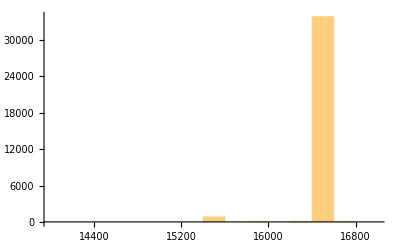

```mathematica
Histogram[Sort[fullmeta[[#,4]]&/@Range[Length@fullmeta]],{14000,17000,200}]
```

```mathematica
HistogramList[haplometa[[;;,4]],{14000,17000,200}]
```

{{14000,14200,14400,14600,14800,15000,15200,15400,15600,15800,16000,16200,16400,16600,16800,17000},{0,0,0,0,0,0,0,837,0,0,0,3,31016,4,0}}

```mathematica
allhaploindices//Length
```

2300

```mathematica
haploIndices//Length
```

23

```mathematica
haplo={"H","L","M","U","B","D","J","T","K","C","A","R","F","N","I","V","W","X","E","G","Q","Z","Y"};
haplo={"L1","L2","L3"};
haploSample={50,50,50};
```

```mathematica
SeedRandom[12345];
filteredHaplo = Table[
Select[haplometa,(haplo[[i]]==StringTake[#[[5,3]],{1,Min[StringLength@haplo[[i]],StringLength[#[[5,3]]]]}])&&(#[[4]]>16000)&]
,{i,1,Length@haplo}];
Print[Dimensions[#]&/@filteredHaplo];
filteredHaplo = Table[
RandomSample[filteredHaplo[[i]],haploSample[[i]]]
,{i,1,Length@haplo}];
Print[Dimensions[#]&/@filteredHaplo];
accIDs=Flatten@Table[filteredHaplo[[i,;;,3]],{i,1,Length@filteredHaplo}];
```

{{685,5},{874,5},{1137,5}}

{{50,5},{50,5},{50,5}}

```mathematica
newDir="ref_pairwise_l1_l2_l3";
(* CGR READ-BUILD *)
SetDirectory[NotebookDirectory[]];Needs["GenResearch`"];
If[!FileExistsQ[newDir],CreateDirectory[newDir]];
SetDirectory[newDir];cgrOrder={"A","C","G","T"};k=9;
curFileNamesOrder=#<>".fasta"&/@accIDs;
Export["cgrFileOrder.txt",curFileNamesOrder];
If[!FileExistsQ["fasta"],CreateDirectory["fasta"]];
Table[
srcFile=FileNameJoin[{NotebookDirectory[],"allfiles",curFileNamesOrder[[i]]}];
destFile=FileNameJoin[{NotebookDirectory[],newDir,"fasta",curFileNamesOrder[[i]]}];
If[!FileExistsQ[destFile],
CopyFile[srcFile,destFile];
]
,{i,1,Length@curFileNamesOrder}];
SetDirectory[FileNameJoin[{NotebookDirectory[],newDir,"fasta"}]];
Print[AbsoluteTiming[Monitor[allCGRs = {}; flnames =curFileNamesOrder;
For[i = 1, i ≤ Length[flnames], i++, 
	nextNewCGR = linearCGRgrayscale[Import[flnames[[i]]][[1]], cgrOrder, k];
	AppendTo[allCGRs, nextNewCGR];
];
,
TableForm[{StringJoin["Reading file: ", ToString[{i,Length[flnames]}], " - ", flnames[[i]]], 
ProgressIndicator[Dynamic[i], {1, Length[flnames]}]}]];
"reading "<>ToString[i-1]<>" files"]]; 
SetDirectory[NotebookDirectory[]];SetDirectory[newDir];Put[Compress@allCGRs,"allCGRs.dat"];Print[Dimensions@allCGRs];
(**)
Print[Dynamic[{i,j}]];distMat=Table[-1,{i,1,Length@allCGRs},{j,1,Length@allCGRs}];
Table[
distMat[[i,j]]=ApproxInfoDist[allCGRs[[i]],allCGRs[[j]]];
distMat[[j,i]]=distMat[[i,j]];
,{i,1,Length@allCGRs},{j,i,Length@allCGRs}];
SetDirectory[NotebookDirectory[]];SetDirectory[newDir];Put[Compress@distMat,"distMat.dat"];Print[Dimensions@distMat];
(**)
filteredDistances=distMat;
(* mds call *)
Print["go for mds"];
AbsoluteTiming[
mdsres=mds[filteredDistances,8,2];
pts=mdsres[[1]];Print["mds returned coord's for ",Length[pts]," points."];Print["First 10 Eigenvalues=",Take[mdsres[[3]],Min[5,Length[pts]]]];
Print[mdsres[[2]]//MatrixForm];
];
Print["finished mds"];
(* scaling *)
ptsOld=pts;ptsToBeScaled=Transpose[pts];
ptsX=ptsToBeScaled[[1]];ptsY=ptsToBeScaled[[2]];ptsZ=ptsToBeScaled[[3]];
ptsXScaled=Rescale[ptsX,{Min[ptsX],Max[ptsX]},{-1,1}];
ptsYScaled=Rescale[ptsY,{Min[ptsY],Max[ptsY]},{-1,1}];
ptsZScaled=Rescale[ptsZ,{Min[ptsZ],Max[ptsZ]},{-1,1}];
ptsScaled=Transpose[{ptsXScaled,ptsYScaled,ptsZScaled}];
pts=ptsScaled;ptsMST3D=ptsScaled;
Print["finished scaling"];
graphicsofpts3d={};
tmp=Flatten[filteredHaplo,1];
For[i=1,i≤Length@accIDs,i++,
 AppendTo[graphicsofpts3d,
Annotation[Text["",pts[[i]]],
tmp[[i]]
,"Mouse"]
];
];
(**)
x=Dimensions[#]&/@filteredHaplo;
t=x[[;;,1]];
q=Table[Sum[t[[j]],{j,1,i}],{i,1,Length@t}];
x1=Drop[Prepend[q,0],-1]+1;
x2=q;
ranges=Transpose[{x1,x2}];
newpts=Take[pts,#]&/@ranges;
(**)
Print[Show[ListPointPlot3D[newpts(*pts*),PlotStyle->Automatic,PlotRange->All,BoxRatios->{1, 1, 1}],Graphics3D[graphicsofpts3d]]];
Print[Dynamic[mousepos=MouseAnnotation[];
info={"ID","Organism","Len","Acc","Haplo"};
info=Style[#,Black,Bold,Medium]&/@info;
If[mousepos===Null,,disp={info,{ToString[mousepos[[1]]],ToString[mousepos[[2]]],ToString[mousepos[[3]]],ToString[mousepos[[4]]],mousepos[[5]]}}];
Grid[Transpose[disp],Alignment->{{Left,Left},{Center,Center}},Background->LightBlue,ItemSize->{{Scaled[.2],Scaled[.8]}},Frame->All]]];
```

{13.0827,reading 150 files}

{150,512,512}

{150,150}

go for mds

mds returned coord's for 150 points.

First 10 Eigenvalues={0.137447,0.0426201,0.0289685,0.0138973,0.0129454}

0

finished mds

finished scaling

-Graphics3D-